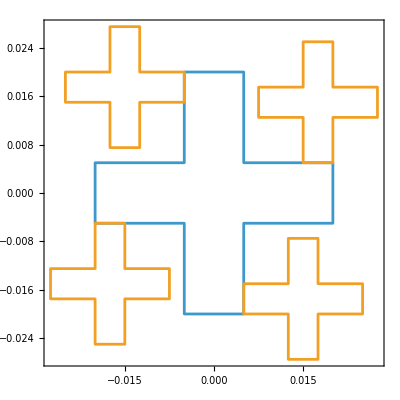

```mathematica
ParamValsForPlotting={hc->0.04,wc->0.01,hw->0.02,ww->0.005};

RegCore=Polygon[{
{wc/2,hc/2},
{-wc/2,hc/2},
{-wc/2,hc/8},
{-2wc, hc/8},
{-2 wc,-hc/8},
{-wc/2,-hc/8},
{-wc/2, -hc/2},
{wc/2, -hc/2},
{wc/2, -hc/8},
{2wc, -hc/8},
{2wc,hc/8},
{wc/2,hc/8},
{wc/2, hc/2}}];


RegWing =RegionUnion[
Polygon[{
{-ww,hw},
{-2.5ww,hw},
{-2.5ww,11/8hw},
{-3.5 ww,11/8 hw},
{-3.5 ww, hw},
{-5 ww, hw},
{-5 ww,0.75hw},
{-3.5ww,0.75 hw},
{-3.5 ww,3/8 hw},
{-2.5ww,3/8 hw},
{-2.5 ww,0.75 hw},
{- ww,0.75 hw},
{- ww, hw}
}],
Polygon[{
{-4ww,-hw/4},
{-4ww,-5/8hw},
{-5.5ww,-5/8hw},
{-5.5ww,-7/8 hw},
{-4ww,-7/8 hw},
{-4 ww,-5/4 hw},
{-3ww,-5/4 hw},
{-3ww,-7/8hw},
{-1.5ww,-7/8hw},
{-1.5ww,-5/8 hw},
{-3 ww,-5/8 hw},
{-3ww,-hw/4},
{-4ww,-hw/4}
}],
Polygon[{
{ww,-hw},
{2.5 ww,-hw},
{2.5 ww,-11/8 hw},
{3.5 ww,-11/8 hw},
{3.5 ww,- hw},
{5ww,- hw},
{5 ww,-0.75 hw},
{3.5 ww,-0.75 hw},
{3.5 ww,- 3/8hw},
{2.5 ww,-3/8 hw},
{2.5 ww,-0.75 hw},
{ww, -0.75hw},
{ww,-hw}
}],
Polygon[{
{4 ww, hw/4},
{4 ww,5/8hw},
{5.5 ww,5/8 hw},
{5.5 ww,7/8hw},
{4ww,7/8 hw},
{4 ww,1.25hw},
{3 ww,1.25hw},
{3ww,7/8hw},
{1.5 ww,7/8 hw},
{1.5 ww,5/8hw},
{3 ww,5/8 hw},
{3 ww, hw/4},
{4 ww,hw/4}}]
];

RegionPlot[{RegCore/.ParamValsForPlotting,RegWing/.ParamValsForPlotting},AspectRatio->Automatic,PlotStyle->None]
```

```mathematica
Jc2=NIntegrate[x^2+y^2,{x,y}∈RegCore/. ParamValsForPlotting]
Jw2=NIntegrate[x^2+y^2,{x,y}∈RegWing/. ParamValsForPlotting]
```

1.11667×10^-7

3.99792×10^-7

```mathematica
Ac=NIntegrate[1,{x,y}∈RegCore/. ParamValsForPlotting]
Aw=NIntegrate[1,{x,y}∈RegWing/. ParamValsForPlotting]
```

0.0007

0.0007

```mathematica
Jc4=NIntegrate[(x^2+y^2)^2,{x,y}∈RegCore/. ParamValsForPlotting]
Jw4=NIntegrate[(x^2+y^2)^2,{x,y}∈RegWing/. ParamValsForPlotting]
```

2.74389×10^-11

2.58596×10^-10